```mathematica
plotstuff[a_]:=
(Graphics[{Circle[#[[1]],0.5],Text[#[[2]],#[[1]]]}&/@({Partition[a,2],Table[ToString[k],{k,1,7}]}//Transpose)]);
plotstuffsized[a_,size_]:=Image[plotstuff[a],ImageSize->{size,size}];
showPhi[phi_,size_:100]:=ImageAssemble[Partition[Table[plotstuffsized[phi[[Floor[k]]],size],{k,1,stringLength,stringLength/9}],3]];
distance[a_,b_]:=Norm[a-b,2];
```

```mathematica
stringLength=100;
postable=Partition[Import["/home/abe/uu/comsys/ComSys/pos.txt","table"],stringLength];
energytable=Import["/home/abe/uu/comsys/ComSys/energy.txt","table"];
nIters=Length[postable];
GraphicsRow[{showPhi[postable[[1]]],showPhi[postable[[-1]]]},ImageSize->600]
```

-Graphics-

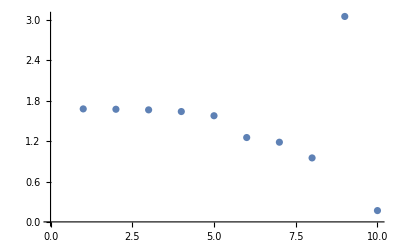

```mathematica
(*Maximum difference between distances between states in string (should be near zero)*)
Table[(Max[#]-Min[#])&[Norm/@(postable[[k]]//Differences)],{k,1,Length[postable]}]//ListPlot
```

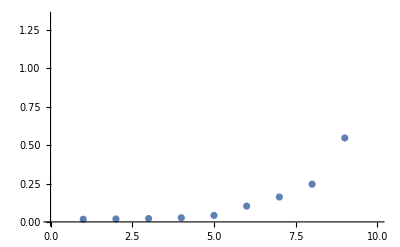

```mathematica
(*Rate of change*)
Table[distance[postable[[j]][[k]],postable[[j]][[k+1]]],{k,1,Length[postable[[1]]]-1},{j,1,nIters}][[50]]//ListPlot
```

```mathematica
Manipulate[ListPlot[Table[distance[postable[[j]][[k]],postable[[j]][[k+1]]],{k,1,Length[postable[[1]]]-1}],PlotRange->Full],{j,1,nIters,1}]
```

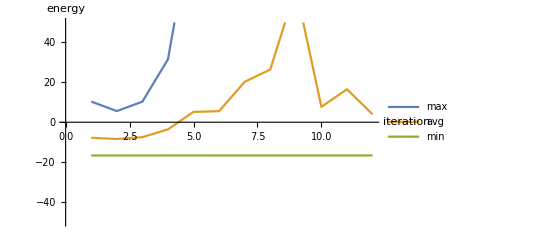

```mathematica
energyplot=ListPlot[{Max/@energytable,Mean/@energytable,Min/@energytable},PlotRange->{Automatic,{-50,50}},Joined->True,AxesLabel->{"iteration","energy"},PlotLegends->{"max","avg","min"}]
```

```mathematica
animation=ParallelTable[showPhi[postable[[iter]]],{iter,1,nIters,1}];
```

```mathematica
Animate[animation[[k]],{k,1,Length[animation],1}]
```

```mathematica
(*Export["moving_particles.gif",animation,ImageSize->{60*3,60*3}]*)
```

moving_particles.gif

```mathematica
(*Export["energy_vs_iteration.png",energyplot]*)
```

energy_vs_iteration.png

```mathematica
(1+2g)x^2-(1-2g)y^2-4g x y//FullSimplify
```

(x-y) (x+2 g x+y-2 g y)

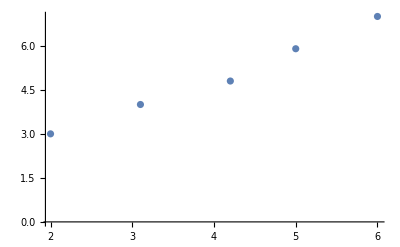

```mathematica
{{2,3},{3+1/10,4},{4+1/5,5-1/5},{5,6-1/10},{6,7}}//ListPlot
```

```mathematica
phi={{2,3},{3+1/10,4},{4+1/5,5-1/5},{5,6-1/10},{6,7}}
```

{{2,3},{31/10,4},{21/5,24/5},{5,59/10},{6,7}}

```mathematica
alphaApprox=Flatten[{0,Table[((phi[[i+1]]-phi[[i-1]]).phi[[i]])/(Norm[phi[[i+1]]-phi[[i-1]]]^2),{i,2,Length[phi]-1}],0}]
```

{0,701/404,45/19,1099/404,0}

```mathematica
Table[{alphaApprox[[k]],1,-alphaApprox[[k]]},{k,1,Length[phi]}]
```

{{0,1,0},{701/404,1,-701/404},{45/19,1,-45/19},{1099/404,1,-1099/404},{0,1,0}}

```mathematica
m={{1,0,0,0,0},{(701x)/404,1,-(701x)/404,0,0},{0,(45x)/19,1,-(45x)/19,0},{0,0,(1099x)/404,1,-(1099x)/404},{0,0,0,0,1}};
```

```mathematica
m=1/2{{2,0,0,0,0},{1+x,2,1-x,0,0},{0,1+x,2,1-x,0},{0,0,1+x,2,1-x},{0,0,0,0,2}};
```

```mathematica
(((Inverse[m]/.{x->0}))*Transpose[{{2,3},{4,3/2},{5,2},{7,2},{8,3}}])
```

{{2,4,5,7,8},{3,3/2,2,2,3}} {{1,0,0,0,0},{-3/4,3/2,-1,1/2,-1/4},{1/2,-1,2,-1,1/2},{-1/4,1/2,-1,3/2,-3/4},{0,0,0,0,1}}

```mathematica
A=((Inverse[m]));
```

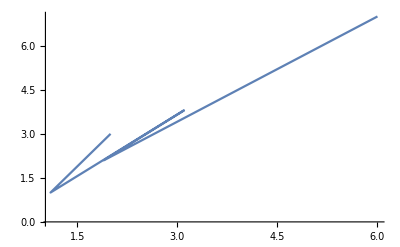
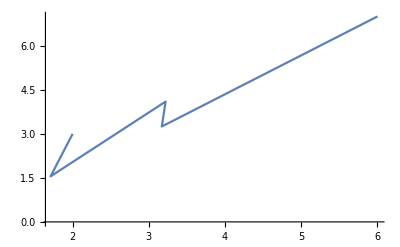
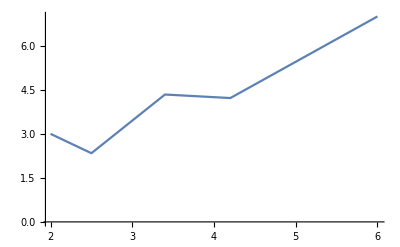
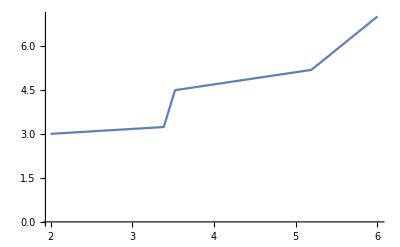
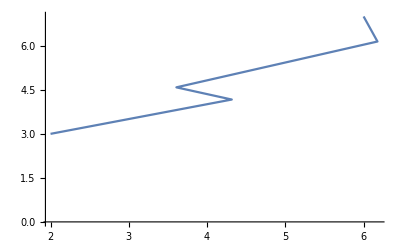

```mathematica
Table[ListLinePlot[A.phi],{x,1,5}]
```

```mathematica
ListLinePlot[(A/.{x->4}).phi]
```

-Graphics-

```mathematica
x,y,z
```

```mathematica
yo
```

```mathematica
y==yo+g(z-x)
```

y==yo+g (-x+z)

```mathematica
Norm[x-y]==Norm[y-z]
```

Norm[x-y]==Norm[y-z]

```mathematica
Norm[yo+g(z-x)-x]==Norm[yo+g(z-x)-z]
```

Norm[-x+yo+g (-x+z)]==Norm[yo-z+g (-x+z)]

```mathematica
y0={y01,y02};
z={z1,z2};
x={x1,x2};
y={y1,y2};
```

```mathematica
y0=.;
z=.;
x=.;
y=.;
```

```mathematica
Transpose[yo+g(z-x)-x].(yo+g(z-x)-x)
```

Transpose[{-x1+yo+g (-x1+z1),-x2+yo+g (-x2+z2)}].{-x1+yo+g (-x1+z1),-x2+yo+g (-x2+z2)}

```mathematica
Transpose[yo+g(z-x)-z].(yo+g(z-x)-z)
```

Transpose[{yo-z1+g (-x1+z1),yo-z2+g (-x2+z2)}].{yo-z1+g (-x1+z1),yo-z2+g (-x2+z2)}

```mathematica
(Transpose[yo]+g Transpose[z]-g Transpose[x]-Transpose[x])*(yo+g(z-x)-x)==(Transpose[yo]+g Transpose[z]-g Transpose[x]-Transpose[z])*(yo+g(z-x)-z)//FullSimplify
```

(x+2 g x-yo-2 g z) Transpose[x]+(-x+z) Transpose[yo]+(-2 g x+yo-z+2 g z) Transpose[z]==0

```mathematica
(x+2 g x-yo-2 g z) Transpose[x]+(-x+z) Transpose[yo]+(-2 g x+yo-z+2 g z) Transpose[z]==0//Expand
```

x Transpose[x]+2 g x Transpose[x]-yo Transpose[x]-2 g z Transpose[x]-x Transpose[yo]+z Transpose[yo]-2 g x Transpose[z]+yo Transpose[z]-z Transpose[z]+2 g z Transpose[z]==0

```mathematica
x Transpose[x]+2 g x Transpose[x]-yo Transpose[x]-2 g z Transpose[x]-yo Transpose[x]+yo Transpose[z]-2 g z Transpose[x]+yo Transpose[z]-z Transpose[z]+2 g z Transpose[z]==0//FullSimplify
```

```mathematica
Solve[(x+2 g x-2 (yo+2 g z)) Transpose[x]+(2 yo+(-1+2 g) z) Transpose[z]==0,yo]
```

{{yo→(x Transpose[x]+2 g x Transpose[x]-4 g z Transpose[x]-z Transpose[z]+2 g z Transpose[z])/(2 (Transpose[x]-Transpose[z]))}}

```mathematica
(x^2+2 g x^2-4 g z Transpose[x]-z^2+2 g z^2)/(2 (Transpose[x]-Transpose[z]))//FullSimplify
```

((1+2 g) x^2+(-1+2 g) z^2-4 g z Transpose[x])/(2 (Transpose[x]-Transpose[z]))

```mathematica
2(x-z)yo==(2g+1)x^2+(2g-1)z^2-4g z x
```

```mathematica
(2g+1)x^2+(2g-1)z^2-4g z x//FullSimplify
```

(x-z) (x+2 g x+z-2 g z)

```mathematica
yo== (x+2 g x+z-2 g z)/2
```

```mathematica
(x+2 g x+z-2 g z)/2//FullSimplify
```

```mathematica
((1+2g)x+(1-2g)z)/2
```

```mathematica
m=1/2{{2,0,0,0,0},{1+2g,1,1-2g,0,0},{0,1+2g,1,1-2g,0},{0,0,1+2g,1,1-2g},{0,0,0,0,2}};
```

```mathematica
m//MatrixForm
```

(1 | 0 | 0 | 0 | 0
1/2 (1+2 g) | 1/2 | 1/2 (1-2 g) | 0 | 0
0 | 1/2 (1+2 g) | 1/2 | 1/2 (1-2 g) | 0
0 | 0 | 1/2 (1+2 g) | 1/2 | 1/2 (1-2 g)
0 | 0 | 0 | 0 | 1)

```mathematica
ultiMatrix=(Inverse[m]);
```

```mathematica
phi//ListPlot
```

-Graphics-

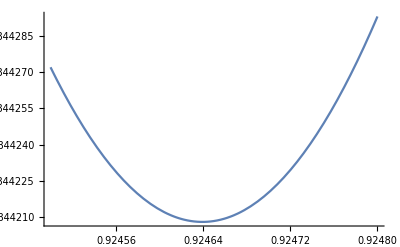

```mathematica
Plot[Norm/@(((ultiMatrix).phi)//Differences)//N//Variance,{g,0.9245,0.9248}]
```

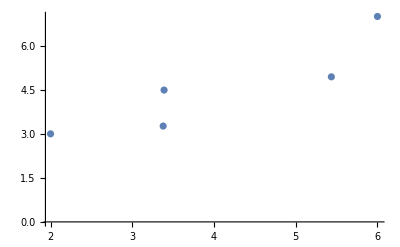

```mathematica
((ultiMatrix/.{g->0.924}).phi)//ListPlot
```

```mathematica
Solve[x^2 b^2+(1-x)^2 bp^2+a^2+2x(1-x)bbp-2x ba-2(1-x)bpa==r^2,x]//FullSimplify
```

{{x→(ba-bbp+bp^2-bpa-1/2 √(4 (ba-bbp+bp^2-bpa)^2-4 (b^2-2 bbp+bp^2) (a^2+bp^2-2 bpa-r^2)))/(b^2-2 bbp+bp^2)},{x→(ba-bbp+bp^2-bpa+1/2 √(4 (ba-bbp+bp^2-bpa)^2-4 (b^2-2 bbp+bp^2) (a^2+bp^2-2 bpa-r^2)))/(b^2-2 bbp+bp^2)}}